```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
bottomx=Import["bottom_displacement_x.txt","Table"];
bottomy=Import["bottom_displacement_y.txt","Table"];
topx=Import["top_displacement_x.txt","Table"];
topy=Import["top_displacement_y.txt","Table"];
```

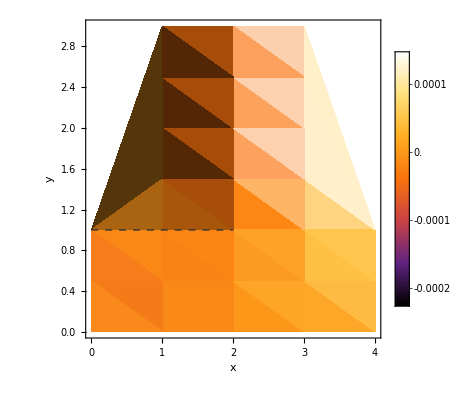

x5.pdf

```mathematica
allDatax=Join[bottomx,topx];
plotx=ListDensityPlot[allDatax,Mesh->None,ColorFunction->"SunsetColors",Frame->True,Axes->False,FrameLabel->{"x","y"},PlotLegends->Automatic,PlotRange->All,Epilog->{{Dashed,GrayLevel[0.2],AbsoluteThickness[1],Line[{{0,1},{2,1}}]}}]
Export["x5.pdf", plotx]
```

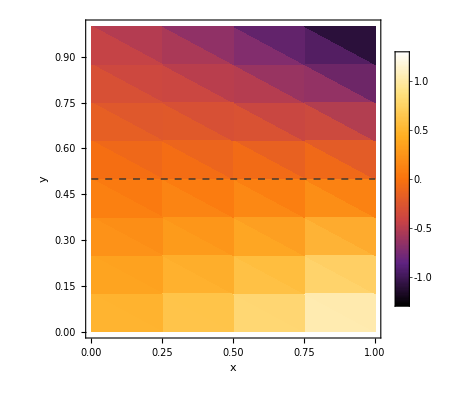

y5.pdf

```mathematica
allDatay=Join[bottomy,topy];
ploty=ListDensityPlot[allDatay,Mesh->None,ColorFunction->"SunsetColors",Frame->True,Axes->False,FrameLabel->{"x","y"},PlotLegends->Automatic,PlotRange->All,Epilog->{{Dashed,GrayLevel[0.2],AbsoluteThickness[1],Line[{{0,0.5},{1,0.5}}]}}]
Export["y5.pdf", ploty]
```

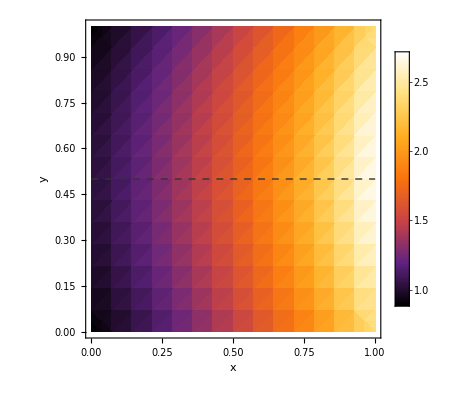

exactx.pdf

```mathematica
ux[x_,y_]:=Exp[x]Cos[y - 0.5]; 
exactx=DensityPlot[ux[x,y],{x,0,1},{y,0,1},Mesh->None,ColorFunction->"SunsetColors",Frame->True,Axes->False,FrameLabel->{"x","y"},PlotLegends->Automatic,PlotRange->All,Epilog->{{Dashed,GrayLevel[0.2],AbsoluteThickness[1],Line[{{0,0.5},{1,0.5}}]}}]
Export["exactx.pdf", exactx]
```

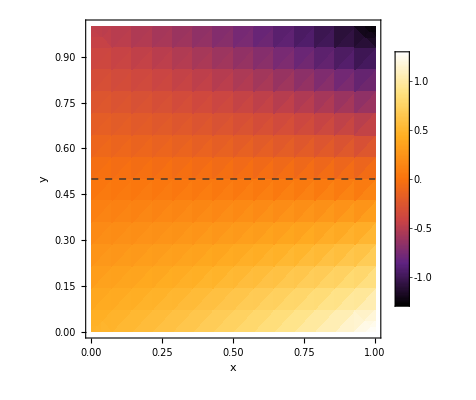

exacty.pdf

```mathematica
uy[x_,y_]:=-Exp[x]Sin[y - 0.5]; 
exacty=DensityPlot[uy[x,y],{x,0,1},{y,0,1},Mesh->None,ColorFunction->"SunsetColors",Frame->True,Axes->False,FrameLabel->{"x","y"},PlotLegends->Automatic,PlotRange->All,Epilog->{{Dashed,GrayLevel[0.2],AbsoluteThickness[1],Line[{{0,0.5},{1,0.5}}]}}]
Export["exacty.pdf", exacty]
```

```mathematica
e = 21 * 10^10;
nu = 0.3;
mu=e/(2*(1+nu));
lambda=e*nu/((1+nu)*(1-2*nu));
```

```mathematica
reg[x_,y_]:=(0<=x<=4&&0<=y<=1)||(0<=x<=2&&1<=y<=3)
```

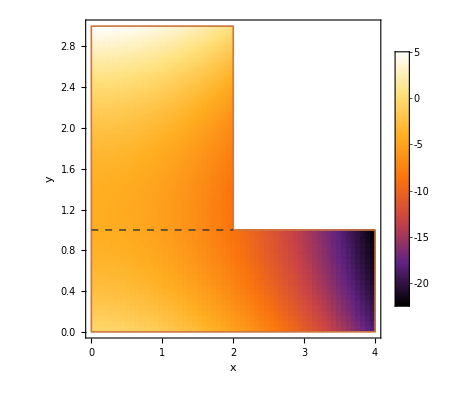

exactx_dif_bodies.pdf

```mathematica
ux2[x_,y_]:=-((lambda+2.0*mu)/(2.0*lambda))*x*x-(4.0*(lambda+mu)/lambda)*y+((3.0*lambda+4.0*mu)/(2.0*lambda))*y*y;

exactx2=DensityPlot[ux2[x,y],{x,0,4},{y,0,3},RegionFunction->Function[{x,y,z},(0<=x<=4&&0<=y<=1)||(0<=x<=2&&1<=y<=3)],Mesh->None,ColorFunction->"SunsetColors",Frame->True,Axes->False,FrameLabel->{"x","y"},PlotLegends->Automatic,PlotRange->All,BoundaryStyle->{Black,AbsoluteThickness[1.2]},PlotPoints->60,MaxRecursion->2,Epilog->{{Dashed,GrayLevel[0.2],AbsoluteThickness[1],Line[{{0,1},{2,1}}]}}]
Export["exactx_dif_bodies.pdf", exactx2]
```

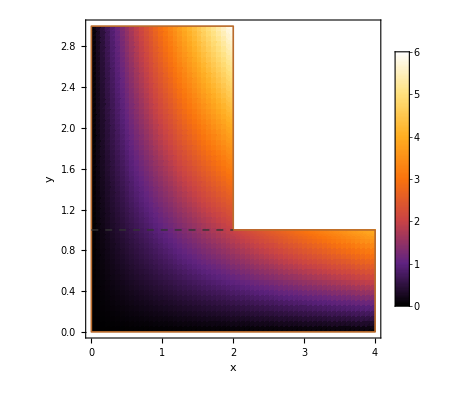

exacty_dif_bodies.pdf

```mathematica
uy2[x_,y_]:=x * y;

exacty2=DensityPlot[uy2[x,y],{x,0,4},{y,0,3},RegionFunction->Function[{x,y,z},(0<=x<=4&&0<=y<=1)||(0<=x<=2&&1<=y<=3)],Mesh->None,ColorFunction->"SunsetColors",Frame->True,Axes->False,FrameLabel->{"x","y"},PlotLegends->Automatic,PlotRange->All,BoundaryStyle->{Black,AbsoluteThickness[1.2]},PlotPoints->60,MaxRecursion->2,Epilog->{{Dashed,GrayLevel[0.2],AbsoluteThickness[1],Line[{{0,1},{2,1}}]}}]
Export["exacty_dif_bodies.pdf", exacty2]
```

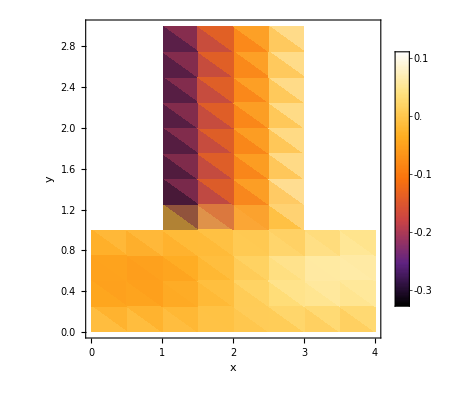

ux_dif_bodies.pdf

```mathematica
bottomx=Import["bottom_displacement_x.txt","Table"];
topx=Import["top_displacement_x.txt","Table"];

datax=Join[bottomx,topx];

plotx=Show[ListDensityPlot[datax,Mesh->None,ColorFunction->"SunsetColors",Frame->True,Axes->False,FrameLabel->{"x","y"},PlotLegends->Automatic,PlotRange->All], Graphics[{White,Rectangle[{3,1},{4,3}]}], Graphics[{White,Rectangle[{0,1},{1,3}]}]]
Export["ux_dif_bodies.pdf",plotx]
```

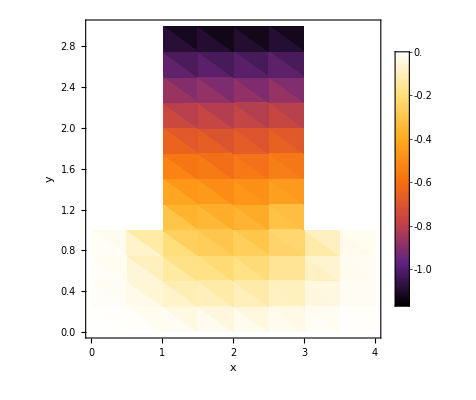

uy_dif_bodies.pdf

```mathematica
bottomy=Import["bottom_displacement_y.txt","Table"];
topy=Import["top_displacement_y.txt","Table"];

datay=Join[bottomy,topy];

ploty=Show[ListDensityPlot[datay,InterpolationOrder->1,Mesh->None,ColorFunction->"SunsetColors",Frame->True,Axes->False,FrameLabel->{"x","y"},PlotLegends->Automatic,PlotRange->All],Graphics[{White,Rectangle[{3,1},{4,3}]}], Graphics[{White,Rectangle[{0,1},{1,3}]}]]
Export["uy_dif_bodies.pdf", ploty]
```